```mathematica
SetDirectory[NotebookDirectory[]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"utility_generator_functions.nb"}]]
```

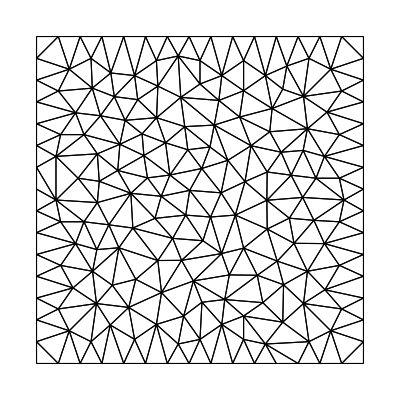

```mathematica
configPath="D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\";
Mcm=1.28;
(*TO DO: Fix the borders and source and MCM*)
left=-8;
right=8;
lower=-8;
middle=-11;
upper=8;
region=Rectangle[{left,lower},{right,upper}];
Needs["NDSolve`FEM`"];
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement","MeshQualityGoal"->0.9,MaxCellMeasure->Mcm];
Show[em["Wireframe"]]
elements=em["MeshElements"][[1,1]];
nodes = em["Coordinates"];
elementsLen=Length[elements];
```

```mathematica
(*Check if mesh is ok*)
t = Table[{nodes[[i]],1},{i,1,Length[nodes]}];
(*Print["table: ",table];*)
intF = Interpolation[t,InterpolationOrder->1];
```

```mathematica
Length[elements]
Length[nodes]
getLongestEdgeInMesh[nodes,elements]
minLen
```

62988

31895

0.209616

0.087843

```mathematica
setUpMeshForCpp[nodes,elements]
```

Exported nodes and elements

Found source

Resolved seismograh points

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[cavity,{-5.33333,-7.64444}].

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[cavity,{-7.64444,-7.64444}].

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[cavity,{-7.11111,-7.11111}].

General::stop: Further output of RegionMember::regp will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[List,=].

sourceElement

seismographIndices

mcm

tau

depths

left

right

cavityIndices

```mathematica
(*TIME LOG 50m  *)
```

```mathematica
initial[x_,y_]:=Module[{ux,uy},(
ux=-2*x/((x^2+1)^2*(y^2+1));
uy=-2*y/((y^2+1)^2*(x^2+1));
ux^2+uy^2
)]
u0xy[x_,y_]:=Module[{ux,uy},(
ux=-2*x/((x^2+1)^2*(y^2+1));
uy=-2*y/((y^2+1)^2*(x^2+1));
{ux,uy}
)]
```

```mathematica
matrixB=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_snapshots_0.08.csv","CSV"];
Dimensions[matrixB]
```

{5,42180}

```mathematica
nodes=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\nodes.csv","CSV"];
```

```mathematica
calculatePlot[matrixB,nodes];
```

```mathematica
(*calculatePlot[initialTable,nodes];*)
```

```mathematica
smallRegion=Rectangle[{-3,-3},{3,3}];
```

```mathematica
(*Manipulate[Plot3D[ihat[[j]][x,y],{x,y}∈smallRegion,PlotRange->All],{j,1,Length[ihat],1}]*)
```

```mathematica
(*Analytical formula*)
```

```mathematica
Clear[a]
r=Sqrt[x^2+y^2];
d1=(r^2-a^2-2-2 ⅈ (m x+p y))^(1/2);
d2=(-ⅈ+a n+m x);
d3=(-ⅈ+a n+p y);
s1=m(3ⅈ n a(2-a^2)+2 a^4-3 a^2+r^4-8 r^2+4);
s2= n a^3( 4x-m p y);
s3=3 a^2 (m x^2+ⅈ m p y- m y^2-3 ⅈ x+p x y);
s4=n a (-13x+2 x^3-y^2 x+m p y (-5+4 x^2+y^2)-2 ⅈ (5m x^2+m y^2+3p x y));
s5=-8 p x y-4 ⅈ (x+m p y) (r^2-2);
intb1= (3n a(x-ⅈ m))/(4 d1^5);
intb2= ArcTanh[(ⅈ- p y)/d1]+ArcTanh[(a n-m x+p y)/d1];
ux=(s1+ s2+s3+s4+s5)/(8 d2^2 d3 d1^4)+intb1 intb2;

dy=(r^2-a^2-2-2 ⅈ (m y-p x))^(1/2);
d2y=(-ⅈ+a n+m y);
d3y=(-ⅈ+a n-p x);
s1y=m(3ⅈ n a(2-a^2)+2 a^4-3 a^2+r^4-8 r^2+4);
s2y= n a^3( 4y+m p x);
s3y=3 a^2 (m y^2-ⅈ m p x- m x^2-3 ⅈ y-p x y);
s4y=n a (-13y+2 y^3-x^2 y-m p x (-5+4 y^2+x^2)-2 ⅈ (5m y^2+m x^2-3p x y));
s5y=8 p x y-4 ⅈ (y-m p x) (r^2-2);
intb1y= (3n a(y-ⅈ m))/(4 dy^5);
intb2y= ArcTanh[(ⅈ+ p x)/dy]+ArcTanh[(a n-m y-p x)/dy];
uy=(s1y+ s2y+s3y+s4y+s5y)/(8 d2y^2 d3y dy^4)+intb1y intb2y;
```

```mathematica
test=Table[t^i,{t,0,4,1},{i,1,7,1}]
analyticalSolVector=Table[Sqrt[Re[Sum[ux/.{a->t,x->nodes[[i,1]],y->nodes[[i,2]]},{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2+Re[Sum[uy/.{a->t,x->nodes[[i,1]],y->nodes[[i,2]]},{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2],{t,0,4,1},{i,1,Length[nodes],1}];
```

{{0,0,0,0,0,0,0},{1,1,1,1,1,1,1},{2,4,8,16,32,64,128},{3,9,27,81,243,729,2187},{4,16,64,256,1024,4096,16384}}

```mathematica
(*analyticalSolVector=Table[Sum[Sqrt[Re[Sum[ux/.{a->t,x->nodes[[i,1]],y->nodes[[i,2]]},{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2+Re[Sum[uy/.{a->t,x->nodes[[i,1]],y->nodes[[i,2]]},{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2],{i,1,Length[nodes],1}],{t,0,4,1}];*)
```

```mathematica
n=Length[nodes]
numericalSolVector=Table[Sqrt[matrixB[[j,2*n+2*i-1]]^2+matrixB[[j,2*n+2*i]]^2],{j,1,5},{i,1,Length[nodes]}];
```

10545

```mathematica
err=Table[Norm[analyticalSolVector[[t]]-numericalSolVector[[t]]]/Norm[analyticalSolVector[[t]]],{t,1,5}]
```

{7.19772×10^-7,0.0236707,0.0391174,0.0560207,0.0754831}

```mathematica
Length[nodes]
```

2697

```mathematica
{7.204616122734266*^-7,0.01676874182513794,0.023223102065866266,0.03255434765881855,0.04475645778681954}(*err beshe tolkova*)
```

{7.20462×10^-7,0.0167687,0.0232231,0.0325543,0.0447565}

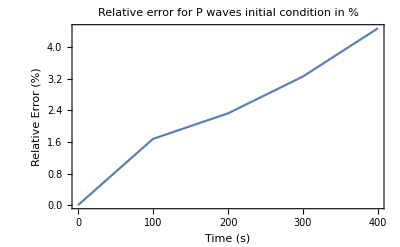

```mathematica
ListLinePlot[{Transpose[{{0,1,2,3,4},err}*100]},Frame->True,
PlotLabel->"Relative error for P waves initial condition in %",
FrameLabel->{"Time (s)","Relative Error (%)"}]
```

```mathematica
(*
n=Length[nodes]
numericalSolVector=Table[Sum[Sqrt[matrixB[[j,2*n+2*i-1]]^2+matrixB[[j,2*n+2*i]]^2],{i,1,Length[nodes]}],{j,1,5}];*)
```

20518

```mathematica
Plot3D[t=1;
analytical =Sqrt[Re[Sum[ux/.a->t,{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2+Re[Sum[uy/.a->t,{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2];analytical(*-ihat[[t+1]][x,y])/(Max[Abs[analytical],10^-8])*),{x,y}∈smallRegion,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[t=3;
ihat[[t+1]][x,y],{x,y}∈smallRegion,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[t=3;
analytical =Sqrt[Re[Sum[ux/.a->t,{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2+Re[Sum[uy/.a->t,{m,-1,1,2},{n,-1,1,2},{p,-1,1,2}]]^2];(analytical-ihat[[t+1]][x,y])/(Max[Abs[analytical],10^-8]),{x,y}∈smallRegion,PlotRange->0.1]
```

-Graphics3D-